```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/zhengyuanyue/OneDrive - The Chinese University of Hong Kong/Courses/PHYS1110 2020-21/Tutorial/Figures

```mathematica
basis=Graphics3D[{Black,Thickness[0.005],Table[Arrow[{{0,0,0},IdentityMatrix[3][[n]]}],{n,1,3}]}];
ω=π/6;θ=π/6;φ=π/4;
newbs[t_]:=0.6Rn[θ,φ,ω t].IdentityMatrix[3]
colors={Red,Blue,Darker[Green]};
direction={Sin[θ]Cos[φ],Sin[θ]Sin[φ],Cos[θ]};
axis=Graphics3D[{Dashed,Blue,Thickness[0.005],Line[{-0.1direction,direction}]}];
labels:=Graphics3D[{Text[Style["Rotation Axis",20,Blue],1.1direction],
Text[Style["x",20,Black,Italic],{1.1,0,0}],
Text[Style["y",20,Black,Italic],{0,1.1,0}],
Text[Style["z",20,Black,Italic],{0,0,1.1}]}];
basis′[t_]:=Graphics3D[{Thickness[0.005],Table[{colors[[n]],Arrow[{{0,0,0},newbs[t][[n]]}]},{n,1,3}]}];
Animate[Show[basis,Evaluate[basis′[t]],axis,labels,Boxed->False, ViewPoint->{Pi,Pi/2,2},PlotRange->{{-0.5,1},{-0.5,1},{-0.3,1}}],{t,0,12,0.01},AnimationRunning->False]
```

Rolling

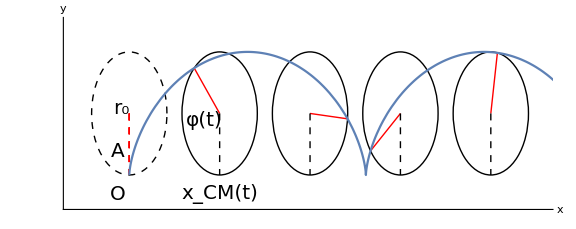

```mathematica
ϕ0=0;ω=1;a=1;b=1;
plate0=Graphics[{Black, Dashed,Circle[{0,a},a]}];
plate[t0_]:=Graphics[{Black, Circle[{ω a t0,a},a]}];
point[t0_]:=Graphics[{Red, Line[{{ω a t0,a},{ω a t0-b Sin[ϕ0+ω t0],a-b Cos[ϕ0+ω t0]}}],Dashed,Line[{{0,a},{-b Sin[ϕ0],a-b Cos[ϕ0]}}]}];
guidelines[t0_]:=Graphics[{Black,Dashed, Line[{{ω a t0,a},{ω a t0,0}}]}];
curve=ParametricPlot[{ω a t-b Sin[ϕ0+ω t],a-b Cos[ϕ0+ω t]},{t,0,11}];
label=Graphics[{Black,Text[Style["A",20],{-0.3,0.4}],Text[Style["O",20],{-0.3,-0.3}],
Text[Style["r_0",Directive[Italic,20]],{-0.2,1.1}],
Text[Style["x_CM(t)",Directive[Italic,20]],{2.4,-0.3}],
Text[Style["φ(t)",20],{2,0.9}]}];
fig=Show[plate0,Table[{plate[t0],point[t0],guidelines[t0]},{t0,2.4,9.6,2.4}],curve,label,Axes->True,AxesLabel->{x,y},Ticks->None,AxesStyle->Directive[20,Black],PlotRange->{{-1.5,11},{-0.5,2.5}},ImageSize->Large]
```

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/zhengyuanyue/OneDrive - The Chinese University of Hong Kong/Courses/PHYS1110 2020-21/Tutorial/Figures

```mathematica
ϕ0=0;ω=0.1;a=1;b=1;ω2=1.0;
Rz[α_]:=({{Cos[α], -Sin[α]}, {Sin[α], Cos[α]}});
square[r_,θ_,φ_]:=Graphics[{{LightBlue,EdgeForm[{Thick,Black}],
Rotate[Rectangle[Rz[θ].{r,0}-0.5],φ,Rz[θ].{r,0}]},
{Darker[Green],Arrow[{{0,0},Rz[θ].{r,0}}]}}];
axis[r_,θ_,b_,φ_]:=Graphics[{Thick,Red,
Arrow[{Rz[θ].{r,0}+Rz[φ].b,Rz[θ].{r,0}+Rz[φ].b+{1,0}}],
Arrow[{Rz[θ].{r,0}+Rz[φ].b,Rz[θ].{r,0}+Rz[φ].b+{0,1}}],
Text[Style["X",Directive[Italic,20]],Rz[θ].{r,0}+Rz[φ].b+{1,0.2}],
Text[Style["Y",Directive[Italic,20]],Rz[θ].{r,0}+Rz[φ].b+{-0.2,1}]}];
cmcurve[r_]:=ParametricPlot[Rz[θ].{r,0},{θ,0,2π},PlotStyle->{Darker[Green],Dashed}];
crcurve[r_,b_]:=ParametricPlot[Rz[θ].{r,0}+Rz[ω2/ω θ].b,{θ,0,2π},PlotStyle->{Red,Dashed}]
title=Graphics[Text[Style["In xy Coordinates",Directive[Italic,20]],{-1.5,2.5}]];
```

```mathematica
r=1.7;b={0.4,0};
fig=Animate[Show[square[r,ω t,ω2 t],axis[r,ω t,b,ω2 t],cmcurve[r],crcurve[r,b],title,
Axes->True,AxesLabel->{x,y},Ticks->None,AxesStyle->Directive[20,Black],PlotRange->{{-3,3},{-3,3}},ImageSize->Large],{t,0,20π},AnimationRunning->False,AnimationRate->0.05]
```

```mathematica
ϕ0=0;ω=0.1;a=1;b=1;ω2=1.0;
Rz[α_]:=({{Cos[α], -Sin[α]}, {Sin[α], Cos[α]}});
square[r_,θ_,φ_]:=Graphics[{{LightBlue,EdgeForm[{Thick,Black}],
Rotate[Rectangle[Rz[θ].{r,0}-0.5],φ,Rz[θ].{r,0}]},
{Darker[Green],Arrow[{{0,0},Rz[θ].{r,0}}]}}];
axis[r_,θ_,b_,φ_]:=Graphics[{Thick,Red,
Arrow[{Rz[θ].{r,0}+Rz[φ].b,Rz[θ].{r,0}+Rz[φ].b+{1,0}}],
Arrow[{Rz[θ].{r,0}+Rz[φ].b,Rz[θ].{r,0}+Rz[φ].b+{0,1}}],
Text[Style["X",Directive[Italic,20]],Rz[θ].{r,0}+Rz[φ].b+{1,0.2}],
Text[Style["Y",Directive[Italic,20]],Rz[θ].{r,0}+Rz[φ].b+{-0.2,1}]}];
cmcurve[r_]:=ParametricPlot[Rz[θ].{r,0},{θ,0,2π},PlotStyle->{Darker[Green],Dashed}];
crcurve[r_,b_]:=ParametricPlot[Rz[θ].{r,0}+Rz[ω2/ω θ].b,{θ,0,2π},PlotStyle->{Red,Dashed}]
title=Graphics[Text[Style["In xy Coordinates",Directive[Italic,20]],{-1.5,2.5}]];
```

```mathematica
Solve[1-6/m/(m+1)==4/5,m]
```

{{m→-6},{m→5}}